{{P[t]→InterpolatingFunction[{{-1., 10.}}, <>][t]}}

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

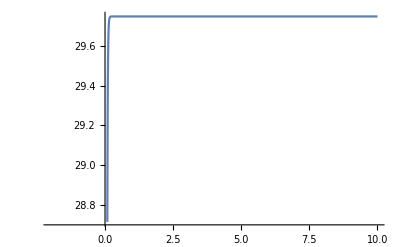

```mathematica
soln1=NDSolve[{P'[t]==P[t](60-2P[t])-15,P[0]==5},P[t],{t,-1,10}]
Plot1=Plot[Evaluate[P[t]/.soln1],{t,-2,10}]
```

{{P[t]→InterpolatingFunction[{{-1., 10.}}, <>][t]}}

InterpolatingFunction::dmval: Input value {-1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

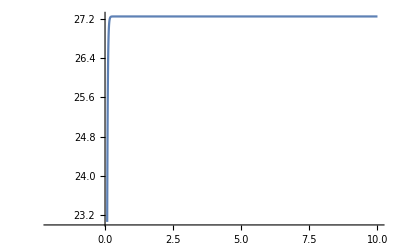

```mathematica
soln2=NDSolve[{P'[t]==P[t](60-2P[t])-150,P[0]==5},P[t],{t,-1,10}]
Plot2 = Plot[Evaluate[P[t]/.soln2],{t,-2,10}]
```

```mathematica
soln3=NDSolve[{P'[t]==P[t](60-2P[t])-200,P[0]==5},P[t],{t,-1,10}]
```

{{P[t]→InterpolatingFunction[{{-1., 10.}}, <>][t]}}

```mathematica
soln4=NDSolve[{P'[t]==P[t](60-2P[t])-250,P[0]==5},P[t],{t,-1,10}]
```

{{P[t]→InterpolatingFunction[{{-1., 10.}}, <>][t]}}

```mathematica
Plot[{Evaluate[P[t]/.soln1],Evaluate[P[t]/.soln2], Evaluate[P[t]/.soln3],Evaluate[P[t]/.soln4]},{t,-1,10}, PlotRange->All, PlotLegends->"Expressions"]
```